```mathematica
persianRugsWeb= Import["https://nazmiyalantiquerugs.com/?orderby=size-desc&product_width_min=1&product_width_max=&product_length_min=1&product_length_max=&product_price_min=0&product_price_max=&product_color=&product_style=&product_origin=persian-rugs&product_sku=&post_type=product&s=&per_page=72", "Images"];
```

Import::htmlimg: Some images could not be imported.

```mathematica
rugs = persianRugsWeb[[4;;-7]];
```

```mathematica
= persianRugsCollage[[;;-7]];
```

```mathematica
prc2 = persianRugsCollage2;
```

```mathematica
prc = ImageCollage[persianRugsCollage2]
```

```mathematica
persianRugs[[5;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
persianRugs2 = Import["https://nazmiyalantiquerugs.com/page/2/?orderby=size-desc&product_width_min=1&product_width_max&product_length_min=1&product_length_max&product_price_min=0&product_price_max&product_color&product_style&product_origin=persian-rugs&product_sku&post_type=product&s&per_page=72", "Images"];
```

Import::htmlimg: Some images could not be imported.

```mathematica
persianRugs2[[5;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
persianRugs3 = Import["https://nazmiyalantiquerugs.com/page/3/?orderby=size-desc&product_width_min=1&product_width_max&product_length_min=1&product_length_max&product_price_min=0&product_price_max&product_color&product_style&product_origin=persian-rugs&product_sku&post_type=product&s&per_page=200", "Images"];
```

Import::htmlimg: Some images could not be imported.

```mathematica
Length[persianRugs3]
```

194

```mathematica
persianRugs4 = Import["https://nazmiyalantiquerugs.com/page/4/?orderby=size-desc&product_width_min=1&product_width_max&product_length_min=1&product_length_max&product_price_min=0&product_price_max&product_color&product_style&product_origin=persian-rugs&product_sku&post_type=product&s&per_page=72", "Images"];
```

```mathematica
persianRugsAll = Import["https://nazmiyalantiquerugs.com/?orderby=size-desc&product_width_min=1&product_width_max&product_length_min=1&product_length_max&product_price_min=0&product_price_max&product_color&product_style&product_origin=persian-rugs&product_sku&post_type=product&s&per_page=585", "Images"];
```

$Aborted

```mathematica
Length[persianRugsAll]
```

594

```mathematica
persianRugsAll[[10;;50]]
```

```mathematica
rugs = persianRugsAll[[4;;588]];
```

```mathematica
img = rugs[[49]]
```

-Graphics-

```mathematica
getSeq[img_]:= Module[{},
bin=LocalAdaptiveBinarize[ImageAdjust[img,0.3],200,{0.9,0,0}];
seq=Reverse[Intersection@@Divisors/@ImageDimensions[img]]]
```

```mathematica
imgs = rugs[[60;;70]];
Map[getSeq, imgs]
```

{{7,1},{1},{2,1},{5,1},{1},{2,1},{14,7,2,1},{2,1},{1},{50,25,10,5,2,1},{1}}

```mathematica
getSeq[img]
```

{10,5,2,1}

```mathematica
{width,height}=ImageDimensions[img]
```

{350,530}

```mathematica
result={width/#,Last@First@ImageLevels@Image[BlockMap[Min,ImageData[bin],{#,#}],"Bit"]}&/@seq;//AbsoluteTiming
```

{0.202552,Null}

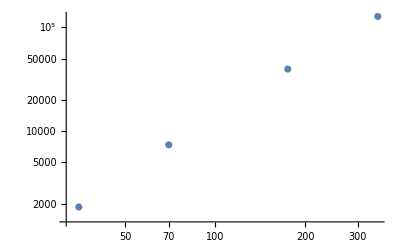

```mathematica
ListLogLogPlot[result]
```

```mathematica
fm=LinearModelFit[Log[result],{1,x},x]
```

FittedModel[…]

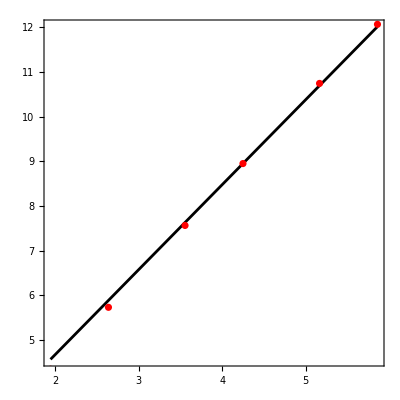

```mathematica
plot=Show[Plot[fm[x],{x,Log[result[[1,1]]],Log[result[[-1,1]]]},PlotStyle->Black],ListLogLogPlot[result,PlotStyle->Red],AspectRatio->1,Axes->False,Frame->True]
```

```mathematica
sz=252;
imgs=Image[BlockMap[Min,ImageData[bin],{#,#}],"Bit"]&/@seq
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
imgs=If[First@ImageDimensions[#]>sz,ImageResize[Image[#,Real],sz],(*downscale as grayscale*)ImageResize[#,sz,Resampling->"Nearest"]]&/@imgs; (*upscale as bitmap*)

frm=Table[ImageCompose[ImageResize[img,252],{im,0.5}],{im,imgs}];

ListAnimate[frm]
```

```mathematica
frames=Table[Row[{Show[plot,AspectRatio->1,ImageSize->336,Epilog->{AbsolutePointSize[10],Red,Point@Log[result[[i]]]}],Image[frm[[i]],Magnification->1]}],{i,Length[imgs]}];
```

```mathematica
ListAnimate[frames]
```

```mathematica
fm=LinearModelFit[Log[result],{1,x},x]
```

FittedModel[…]